## Beams

### Exercise 5.C1

The strategy here is to solve the reactions, then solve the shear force and bending moment in each region of the beam.
We will restrict ourselves to vertical forces and assume that the reactions only occur in the vertical direction.

Consider the general case (with these assumptions):
-Graphics-

To do this, we need equations to solve the areas of the shapes we may need. We will begin with just triangles, rectangles, and trapezoids.

```mathematica
triangleArea[len_,height_]:=1/2*len*height
rectangleArea[len_,height_]:=len*height
trapezoidArea[len_,heightA_,heightB_]:=len*((heightA+heightB)/2)
```

Now we need to calculate the reactions two supports. We only need to keep track of the location in this case (since we assume a vertical direction and we assume everything is acting in the same line of the center of the beam).

As an example:

```mathematica
forceList5C1General={
{"A reaction",aMag,0},
{"B reaction",bMag,lenBeam},
{"Distributed force 1",triangleArea[len1, height1], len1}
};

reactionPiece[mag_,loc_,x_]:=Piecewise[
{{0,x<loc},
{mag,x≥ loc}}
]

simpleForceDist[distA_,distB_,heightA_,heightB_,x_]:=Piecewise[{{0,0*distA<x<distA},{0,x>distB},{((heightB-heightA)/(distB-distA))(x-distA)+heightA,distA<x<distB},{0,x==0}}]
simpleForceDist[dA,dB,ha,hb,x]
```

Piecewise[{{0, 0<x<dA||x>dB}, {ha+((-ha+hb) (-dA+x))/(-dA+dB), dA<x<dB}, {0, True}}]

From there we can invoke equilibrium and calculate the sum of the forces in the y and the moment about A. Now with the reactions, we write the force distributions as piecewise equations. We integrate once to get the shear force and twice to get the bending moment:

(dV(x))/dx=q(x)     and    (dM(x))/dx=V(x) 

We consider the following example:

-Graphics-

```mathematica
forceList5C1={
{"A reaction",aMag,0},
{"B reaction",bMag,Quantity[10, "Feet"]},
{"Distributed force 1",triangleArea[Quantity[3, "Feet"], Quantity[300,"Pounds"/"Feet"]], Quantity[3, "Feet"]},
{"Distributed force 2",rectangleArea[Quantity[2, "Feet"], Quantity[300,"Pounds"/"Feet"]], Quantity[2, "Feet"]},
{"Distributed force 3",rectangleArea[Quantity[5, "Feet"], Quantity[400,"Pounds"/"Feet"]], Quantity[5, "Feet"]}
};
forceNet5C1=Sum[forceList5C1[[i]][[2]],{i,1,Length[forceList5C1]}];
momentNet5C1=Sum[forceList5C1[[i]][[3]]*forceList5C1[[i]][[2]],{i,1,Length[forceList5C1]}];
reactions5C1=Flatten[{aMag,bMag}/.
Solve[forceNet5C1==0&&momentNet5C1==0,{aMag,bMag}]];
aMag=reactions5C1[[1]]
bMag=reactions5C1[[2]]
```

-1795 lb

-1255 lb

We now express the force distributions at functions using:

simpleForceDist[distA_,distB_,lenBeam_,heightA_,heightB_,x_]
and
reactionPiece[mag_,loc_,x_]

```mathematica
Clear[q1,q2,q3,shear,simplef]
lenBeam5=Quantity[10,"Feet"];
q1[x_]:=simpleForceDist[Quantity[0,"Feet"],Quantity[3,"Feet"],Quantity[0,"Pounds"/"Feet"],Quantity[300,"Pounds"/"Feet"],Quantity[x,"Feet"]]
q2[x_]:=simpleForceDist[Quantity[3,"Feet"],Quantity[5,"Feet"],Quantity[300,"Pounds"/"Feet"],Quantity[300,"Pounds"/"Feet"],Quantity[x,"Feet"]]
q3[x_]:=simpleForceDist[Quantity[5,"Feet"],lenBeam5,Quantity[400,"Pounds"/"Feet"],Quantity[400,"Pounds"/"Feet"],Quantity[x,"Feet"]]
q1[x]
q2[x]
q3[x]
(*shear[x_]:=Integrate[q1[s]+q2[s]+q3[s],{s,0,10}]
Plot[shear[x],{x,0,11}]*)
```

Piecewise[{{0, x ft>3 ft}, {100 x lb/ft, 0 ft<x ft<3 ft}, {0, True}}]

Piecewise[{{0, 0 ft<x ft<3 ft||x ft>5 ft}, {300 lb/ft, 3 ft<x ft<5 ft}, {0, True}}]

Piecewise[{{0, 0 ft<x ft<5 ft||x ft>10 ft}, {400 lb/ft, 5 ft<x ft<10 ft}, {0, True}}]

We can also do this with unit-less quantities.

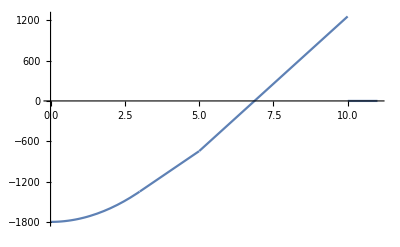

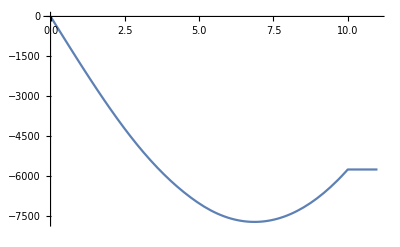

```mathematica
Clear[ayu,byu,shearU]
q1u[x_]:=simpleForceDist[0,3,0,300,x]
q2u[x_]:=simpleForceDist[3,5,300,300,x]
q3u[x_]:=simpleForceDist[5,10,400,400,x]
aMagu=aMag/Quantity[1,"Pounds"];
bMagu=bMag/Quantity[1,"Pounds"];
ayu[x_]:=reactionPiece[aMagu,0,x]
byu[x_]:=reactionPiece[bMagu,10,x]

(*q1u[x];
q2u[x];
q3u[x];
ayu[x];
byu[x];*)

shearU[x_]:=ayu[x]+Integrate[q1u[s]+q2u[s]+q3u[s],{s,0,x},Assumptions->x ∈ Reals]+byu[x]
Plot[shearU[x],{x,0,11}]
bendingU[x_]:=Integrate[shearU[s2],{s2,0,x},Assumptions->x ∈ Reals]
Plot[bendingU[x],{x,0,11}]
```